# Discrete Mechanics

Brian Beckman, April 2024

## Abstract

The school method for numerically solving physics problems is to integrate the Euler-Lagrange equation (https://en.wikipedia.org/wiki/Euler%E2%80%93Lagrange_equation). In this method, one

writes a Lagrangian from the physics for the system

symbolically applies the variational principle, e.g., Hamilton’s Principle, to derive the Euler-Lagrange equation

discretizes time or its surrogate independent variable, e.g., proper time

integrates the discretized equation with respect to that discretized variable given some initial conditions

The school method has many numerical hazards and has spawned an enormous literature.

One of the most interesting alternatives is to discretize the Lagrangian before applying the variational principle, producing an iterable or recursive algebraic equation that can be stepped explicitly or implicitly. There is a growing literature on this alternative. One early reference by Kobilarov and Marsden explains it well and is cited and tested in this note on a foundational case: the undamped simple harmonic oscillator. This example illustrates and supports the un-numbered equations in Section II of the referenced paper.

## Reference

Marin Kobilarov and Jerrold E. Marsden, Discrete Geometric Optimal Control on Lie Groups, IEEE Transactions on Robotics, Vol. 27, No. 4, August 2011.

## Undamped Simple Harmonic Oscillator

```mathematica
ClearAll[L,V,Ld];
```

### Analytical Solution

Potential energy.

```mathematica
V[q_]:=1/2 κ q^2
```

Lagrangian.

```mathematica
L[q_,v_,t_]:=1/2 m v^2-V[q]
```

Second term of the Euler-Lagrange equations: a total derivative of the partial derivative of the Lagrangian L with respect to generalized velocity v, which entails a derivative of mass with respect to time via the chain rule. We insert an explicit correction for constant mass by setting the derivative of mass with respect to time to 0. Non-constant mass would be useful for, say, the rocket equation, but is not pertinent here.

```mathematica
Dt[D[L[q,v,t],v],t]/.{Dt[m,t]->0}
```

m Dt[v,t]

First term of the Euler-Lagrange equations. No explicit assumption of constant spring-force coefficient κ is necessary because this term is just a partial derivative of L with respect to q and does not entail the chain rule.

```mathematica
D[L[q,v,t],q]
```

-q κ

The Euler-Lagrange equations. By inspection, they are equal to the naive Newtonian equations of motion for this undamped oscillator.

```mathematica
deqn=((D[L[q,v,t],q]-(Dt[D[L[q,v,t],v],t]/.{Dt[m,t]->0}/.{v->Dt[q,t]})/.{q->x[t]})==0)
```

-κ x[t]-m x''[t]==0

Mathematica easily solves them. We pick the solution, as a function, from the structure returned by Mathematica’s DSolve.

```mathematica
dsoln=(DSolve[deqn,x,t])[[1,1,2]]
```

Function[{t},C[1] Cos[(t √κ)/(√m)]+C[2] Sin[(t √κ)/(√m)]]

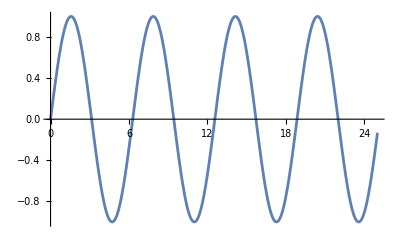

```mathematica
Plot[dsoln[t]/.{κ->1,m->1,C[2]->1,C[1]->0},{t,0,25}]
```

### Discrete Solution

Quadrature of the discrete Lagrangian, which actually has units of action, i.e., energy times time, according to the third, unnumbered equation on page 643 of the reference.

```mathematica
discreteEqn=m((q[k+1]-2q[k]+q[k-1])/h^2)==-1/2((D[V[q],q]/.{q->(q[k-1]+q[k])/2})+(D[V[q],q]/.{q->(q[k]+q[k+1])/2}))
```

(m (q[-1+k]-2 q[k]+q[1+k]))/h^2==1/2 (-1/2 κ (q[-1+k]+q[k])-1/2 κ (q[k]+q[1+k]))

Algebraic solution of the discrete equation for time step k+1 given solutions for time steps k-1 and k. Do not confuse time step k with spring constant κ.

```mathematica
discreteSoln=(Solve[discreteEqn,q[1+k]]//FullSimplify)[[1,1,2]]
```

-q[-1+k]+(2 (4 m-h^2 κ) q[k])/(4 m+h^2 κ)

For integration and plotting, manually substitute the discrete solution (the expression (discreteSoln...) does not work for unknown reasons)

```mathematica
(discreteSoln/.{κ->1,m->1})
```

-q[-1+k]+(2 (4-h^2) q[k])/(4+h^2)

Compare the plot of the analytical solution versus the discrete solution for various choices of the time step, represented by its negative logarithm base 10.

```mathematica
ClearAll[experiment];
experiment[timeSteps_,h_]:=
Module[{k,q,x},
q[k_]:=x[[1+k]];
x=ConstantArray[0,timeSteps+1];
x[[1]]=0;x[[2]]=Sin[h];
For[k=1,k<timeSteps,k++,
x[[k+2]]=-q[-1+k]+(2 (4-h^2) q[k])/(4+h^2)];
GraphicsRow[{
ListLinePlot[x,Frame->True,FrameLabel->{{"Amplitude",""},{"Time Step -- units of h","Discrete Solution"}}],
Plot[dsoln[τ]/.{κ->1,m->1,C[2]->1,C[1]->0},{τ,0,timeSteps h},Frame->True,FrameLabel->{{"Amplitude",""},{"Time Step -- units of 1/h","Analytical Solution"}}]}]];
Manipulate[experiment[25 /10^minuslog10h,10.^minuslog10h],
{minuslog10h,{0,-1,-2,-3,-4}}]
```